```mathematica
沿z轴的电势分布
```

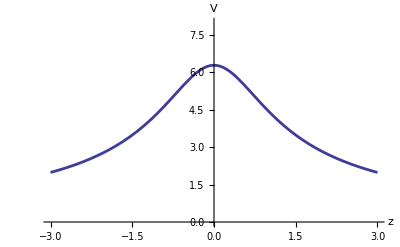

```mathematica
R=1;a=R^2+z^2+ρ^2;b=2ρ*R;
V[z_,ρ_]:=(2 EllipticK[(2 b)/(-a+b)])/(√(a-b))+(2 EllipticK[(2 b)/(a+b)])/(√(a+b));
Plot[V[z,ρ]/.ρ->0,{z,-3R,3*R},PlotRange->{0,8},AxesLabel->{"z","V"},AxesStyle->Thickness[0.004],
PlotStyle->Thickness[0.005]]
Clear[R,a,b,V,z,ρ]
```